# Michael McDonnell Assignment #2 SSI Math 3214 - Calculus of Several Variables 2014/07/01

## 10.3)

{-2+Sin[3 t],4+Cos[3 t]}

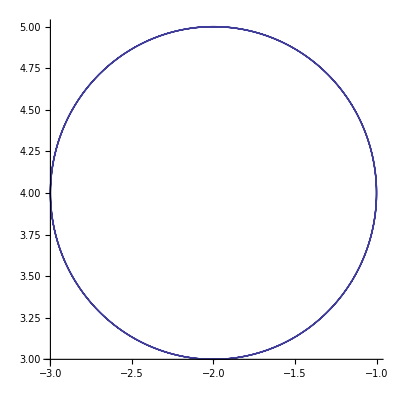

```mathematica
r22[t_]={-2+ Sin[3t],4+ Cos[3t]}
ParametricPlot[r22[t],{t,0,2π}]
```

```mathematica
Animate[ParametricPlot[r22[t],{t,-π,a},PlotRange->{{-4,0},{2,5}}],{a,-π,π}]
```

### 10.4)

{3 Cos[t],2 Sin[t]}

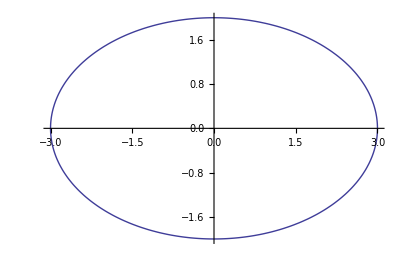

```mathematica
r2[t_]={3Cos[t],2Sin[t]}
ParametricPlot[r2[t],{t,0,2π}]
```

```mathematica
Animate[ParametricPlot[r2[t],{t,π/2,a},PlotRange->{{-3,3},{-2,2}}],{a,π/2,(5π)/2}]
```

## 11.1)

```mathematica
Plot3D[4 x^2+9 y^2,{x,-1,1},{y,-1,1},AxesLabel->{x,y}]
```

-Graphics3D-

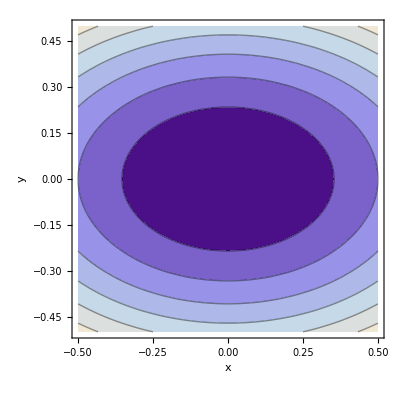

```mathematica
ContourPlot[4 x^2+9 y^2,{x,-.5,.5},{y,-.5,.5},AxesLabel->{x,y}]
```

```mathematica
Plot3D[4 x^2-8x+9 y^2+36y+40,{x,-10,10},{y,-10,10},AxesLabel->{x,y}]
```

-Graphics3D-

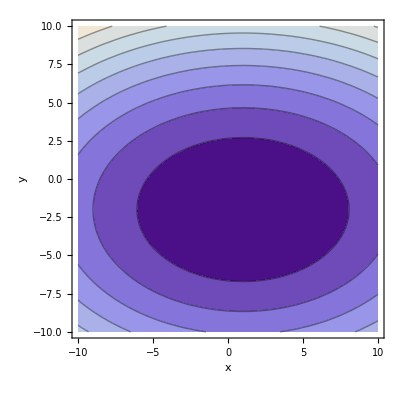

```mathematica
ContourPlot[4 x^2-8x+9 y^2+36y+40,{x,-10,10},{y,-10,10},AxesLabel->{x,y}]
```

## 12.3)

```mathematica
g[θ_,ϕ_]={Cos[θ]Sin[ϕ], 2Sin[θ]Sin[ϕ],3Cos[ϕ]}
ParametricPlot3D[g[θ,ϕ],{θ,0,2π},{ϕ,0,π}, AxesLabel->{x,y,z}]
```

{Cos[θ] Sin[ϕ],2 Sin[θ] Sin[ϕ],3 Cos[ϕ]}

-Graphics3D-